```mathematica
logpart=Log[1+C2*r*omegaf*Sin[h]/(c*gammac)]//.{gammac->(mu/Sin[h]^2)^(1/3)}
eq=gamma2m==C1*((mu-gamma2m)/Sin[h]^2*logpart)^(1/3)//.{gammac->(mu/Sin[h]^2)^(1/3)}
logpart=Log[1+C2*r*omegaf*h/(c*gammac)]//.{gammac->(mu/h^2)^(1/3)}
eq=gamma2m==C1*((mu-gamma2m)/h^2*logpart)^(1/3)//.{gammac->(mu/h^2)^(1/3)}
newgamma2m=eq
```

Log[1+(C2 omegaf r Sin[h])/(c (mu Csc[h]^2)^(1/3))]

gamma2m==C1 ((-gamma2m+mu) Csc[h]^2 Log[1+(C2 omegaf r Sin[h])/(c (mu Csc[h]^2)^(1/3))])^(1/3)

Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]

gamma2m==C1 (((-gamma2m+mu) Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))])/h^2)^(1/3)

gamma2m==C1 (((-gamma2m+mu) Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))])/h^2)^(1/3)

```mathematica
sols=Solve[newgamma2m,gamma2m]
```

{{gamma2m→-((2/3)^(1/3) C1^3 Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))])/((9 C1^3 h^4 mu Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]+√3 √(27 C1^6 h^8 mu^2 Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]^2+4 C1^9 h^6 Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]^3))^(1/3))+((9 C1^3 h^4 mu Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]+√3 √(27 C1^6 h^8 mu^2 Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]^2+4 C1^9 h^6 Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]^3))^(1/3))/(2^(1/3) 3^(2/3) h^2)},{gamma2m→((1+ⅈ √3) C1^3 Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))])/(2^(2/3) 3^(1/3) (9 C1^3 h^4 mu Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]+√3 √(27 C1^6 h^8 mu^2 Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]^2+4 C1^9 h^6 Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]^3))^(1/3))-((1-ⅈ √3) (9 C1^3 h^4 mu Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]+√3 √(27 C1^6 h^8 mu^2 Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]^2+4 C1^9 h^6 Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]^3))^(1/3))/(2 2^(1/3) 3^(2/3) h^2)},{gamma2m→((1-ⅈ √3) C1^3 Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))])/(2^(2/3) 3^(1/3) (9 C1^3 h^4 mu Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]+√3 √(27 C1^6 h^8 mu^2 Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]^2+4 C1^9 h^6 Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]^3))^(1/3))-((1+ⅈ √3) (9 C1^3 h^4 mu Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]+√3 √(27 C1^6 h^8 mu^2 Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]^2+4 C1^9 h^6 Log[1+(C2 h omegaf r)/(c (mu/h^2)^(1/3))]^3))^(1/3))/(2 2^(1/3) 3^(2/3) h^2)}}

```mathematica
consts={C1->2,C2->0.4,omegaf->0.25*c/rfp,mu->10^4/2.3,h->0.021,r->10^(14),rfp->10^6}
logpart//.consts
sols//.consts
(mu-(c*h^(4/3)*mu^(10/3)/(C1^3*C2*r*h*omegaf)))//.consts
```

{C1→2,C2→0.4,omegaf→(0.25 c)/rfp,mu→4347.83,h→0.021,r→100000000000000,rfp→1000000}

6.88792

{{gamma2m→764.989},{gamma2m→-382.495+750.904 ⅈ},{gamma2m→-382.495-750.904 ⅈ}}

-278.366

```mathematica
consts={C1->2,C2->0.4,omegaf->0.25*c/rfp,mu->10^4/2.3,h->0.021,r->10^(10),rfp->10^6}
logpart//.consts
sols//.consts
```

{C1→2,C2→0.4,omegaf→(0.25 c)/rfp,mu→4347.83,h→0.021,r→10000000000,rfp→1000000}

0.0934319

{{gamma2m→191.695},{gamma2m→-95.8477+171.042 ⅈ},{gamma2m→-95.8477-171.042 ⅈ}}

```mathematica
mysol=FullSimplify[sols[[1,1,2]],{h≥0,C1>0,C2>0,omegaf>0,r>0,mu≥1}]
```

(C1 (-2 3^(1/3) C1 Log[1+(C2 h^(5/3) omegaf r)/(c mu^(1/3))]+2^(1/3) (9 h mu Log[1+(C2 h^(5/3) omegaf r)/(c mu^(1/3))]+√3 √(Log[1+(C2 h^(5/3) omegaf r)/(c mu^(1/3))]^2 (27 h^2 mu^2+4 C1^3 Log[1+(C2 h^(5/3) omegaf r)/(c mu^(1/3))])))^(2/3)))/(6^(2/3) h (9 h mu Log[1+(C2 h^(5/3) omegaf r)/(c mu^(1/3))]+√3 √(Log[1+(C2 h^(5/3) omegaf r)/(c mu^(1/3))]^2 (27 h^2 mu^2+4 C1^3 Log[1+(C2 h^(5/3) omegaf r)/(c mu^(1/3))])))^(1/3))

```mathematica
mysol//.{C1->2,C2->0.4,omegaf->0.25*c/rfp}//.{mu->10^4/2.3,h->0.021,r->10^(14),rfp->10^6}
```

764.989

(2^(1/3) (-4 3^(1/3) Log[1+612693. h^(5/3)]+2^(1/3) (39130.4 h Log[1+612693. h^(5/3)]+√3 √(Log[1+612693. h^(5/3)]^2 (5.10397×10^8 h^2+32 Log[1+612693. h^(5/3)])))^(2/3)))/(3^(2/3) h (39130.4 h Log[1+612693. h^(5/3)]+√3 √(Log[1+612693. h^(5/3)]^2 (5.10397×10^8 h^2+32 Log[1+612693. h^(5/3)])))^(1/3))

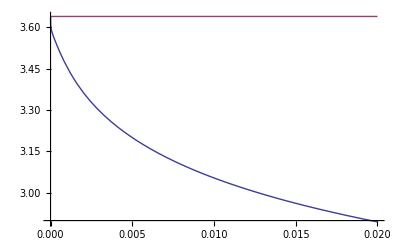

```mathematica
toplot=mysol//.{C1->2,C2->0.4,omegaf->0.25*c/rfp}//.{mu->10^4/2.3,r->10^(14),rfp->10^6}
Plot[{Log[10,toplot],Log[10,10^4/2.3]},{h,0,0.02}]
```

(30.2853 (-4 3^(1/3) Log[1+9.02871×10^-12 10^x]+2^(1/3) (782.609 Log[1+9.02871×10^-12 10^x]+√3 √(Log[1+9.02871×10^-12 10^x]^2 (204159.+32 Log[1+9.02871×10^-12 10^x])))^(2/3)))/(782.609 Log[1+9.02871×10^-12 10^x]+√3 √(Log[1+9.02871×10^-12 10^x]^2 (204159.+32 Log[1+9.02871×10^-12 10^x])))^(1/3)

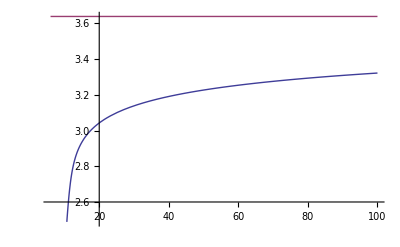

```mathematica
toplot=mysol//.{C1->2,C2->0.4,omegaf->0.25*c/rfp}//.{mu->10^4/2.3,h->0.02,rfp->10^6}//.{r->10^x}
Plot[{Log[10,toplot],Log[10,10^4/2.3]},{x,6,100}]
```

```mathematica
toplot=mysol//.{C1->2,C2->0.4,omegaf->0.25*c/rfp}//.{mu->10^4/2.3,rfp->10^6}
Plot3D[Log[10,toplot],{h,0,0.02},{r,10^6,10^(18)}]
```

(2^(1/3) (-4 3^(1/3) Log[1+6.12693×10^-9 h^(5/3) r]+2^(1/3) (39130.4 h Log[1+6.12693×10^-9 h^(5/3) r]+√3 √(Log[1+6.12693×10^-9 h^(5/3) r]^2 (5.10397×10^8 h^2+32 Log[1+6.12693×10^-9 h^(5/3) r])))^(2/3)))/(3^(2/3) h (39130.4 h Log[1+6.12693×10^-9 h^(5/3) r]+√3 √(Log[1+6.12693×10^-9 h^(5/3) r]^2 (5.10397×10^8 h^2+32 Log[1+6.12693×10^-9 h^(5/3) r])))^(1/3))

-Graphics3D-

```mathematica
myseries=Series[mysol,{r,Infinity,1}]
mysollarger=Normal[myseries]
```

(C1 (-2 3^(1/3) C1 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]+2 3^(1/3) C1 Log[1/r]+2^(1/3) (9 h mu Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-9 h mu Log[1/r]+√3 √((Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r])))^(2/3)))/(6^(2/3) h (9 h mu Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-9 h mu Log[1/r]+√3 √((Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r])))^(1/3))+1/(6^(2/3) h r)C1 (-(((9 c mu^(4/3))/(C2 h^(2/3) omegaf)+(√3 √((Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r])) ((4 c C1^3 mu^(1/3) (Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2)/(C2 h^(5/3) omegaf)+(2 c mu^(1/3) (Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r]) (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r]))/(C2 h^(5/3) omegaf)))/(2 (Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r]))) (-2 3^(1/3) C1 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]+2 3^(1/3) C1 Log[1/r]+2^(1/3) (9 h mu Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-9 h mu Log[1/r]+√3 √((Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r])))^(2/3)))/(3 (9 h mu Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-9 h mu Log[1/r]+√3 √((Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r])))^(4/3))+(-(2 3^(1/3) c C1 mu^(1/3))/(C2 h^(5/3) omegaf)+(2 2^(1/3) ((9 c mu^(4/3))/(C2 h^(2/3) omegaf)+(√3 √((Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r])) ((4 c C1^3 mu^(1/3) (Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2)/(C2 h^(5/3) omegaf)+(2 c mu^(1/3) (Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r]) (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r]))/(C2 h^(5/3) omegaf)))/(2 (Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r]))))/(3 (9 h mu Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-9 h mu Log[1/r]+√3 √((Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r])))^(1/3)))/(9 h mu Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-9 h mu Log[1/r]+√3 √((Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r])))^(1/3))+O[1/r]^2

(C1 (-2 3^(1/3) C1 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]+2 3^(1/3) C1 Log[1/r]+2^(1/3) (9 h mu Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-9 h mu Log[1/r]+√3 √((Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r])))^(2/3)))/(6^(2/3) h (9 h mu Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-9 h mu Log[1/r]+√3 √((Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r])))^(1/3))+1/(6^(2/3) h r)C1 (-(((9 c mu^(4/3))/(C2 h^(2/3) omegaf)+(√3 √((Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r])) ((4 c C1^3 mu^(1/3) (Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2)/(C2 h^(5/3) omegaf)+(2 c mu^(1/3) (Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r]) (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r]))/(C2 h^(5/3) omegaf)))/(2 (Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r]))) (-2 3^(1/3) C1 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]+2 3^(1/3) C1 Log[1/r]+2^(1/3) (9 h mu Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-9 h mu Log[1/r]+√3 √((Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r])))^(2/3)))/(3 (9 h mu Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-9 h mu Log[1/r]+√3 √((Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r])))^(4/3))+(-(2 3^(1/3) c C1 mu^(1/3))/(C2 h^(5/3) omegaf)+(2 2^(1/3) ((9 c mu^(4/3))/(C2 h^(2/3) omegaf)+(√3 √((Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r])) ((4 c C1^3 mu^(1/3) (Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2)/(C2 h^(5/3) omegaf)+(2 c mu^(1/3) (Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r]) (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r]))/(C2 h^(5/3) omegaf)))/(2 (Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r]))))/(3 (9 h mu Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-9 h mu Log[1/r]+√3 √((Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r])))^(1/3)))/(9 h mu Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-9 h mu Log[1/r]+√3 √((Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-Log[1/r])^2 (27 h^2 mu^2+4 C1^3 Log[(C2 h^(5/3) omegaf)/(c mu^(1/3))]-4 C1^3 Log[1/r])))^(1/3))

```mathematica
mysollarger//.{C1->2,C2->0.4,omegaf->0.25*c/rfp}//.{mu->10^4/2.3,h->0.021,r->10^(14),rfp->10^6}
```

764.989

```mathematica
Series[mysollarger,{h,0,1}]
```

$Aborted